```mathematica
Assuming[η>0&&λ>0&&λ>0&&v0>0,DSolve[D[ζ[η],η]+κ ζ[η] == -(v0^2 μ Exp[-2η])/(π λ Sqrt[η] Erf[Sqrt[Y]]^2),ζ[η],η]]
```

{{ζ[η]→ⅇ^(-η κ) C[1]-(ⅇ^(-η κ) v0^2 μ Erfi[√η √(-2+κ)])/(√π √(-2+κ) λ Erf[√Y]^2)}}

```mathematica
v0=1;
μ=1;
λ=1;
Manipulate[Plot[-(ⅇ^(-η κ) v0^2 μ Erf[√η √(2-κ)])/(√π √(2-κ) λ Erf[√Y]^2),{η,0,10}],{κ,1,10},{Y,0.001,10}]
```

```mathematica
Limit[-(ⅇ^(-η κ) v0^2 μ Erfi[√η √(-2+κ)])/(√π √(-2+κ) λ Erf[√Y]^2),κ->2]
```

-(2 ⅇ^(-2 η) √η)/(π Erf[√Y]^2)

```mathematica
-Erfi[√η √(-2+κ)]/(√π √(-2+κ) λ Erf[√Y]^2)
```

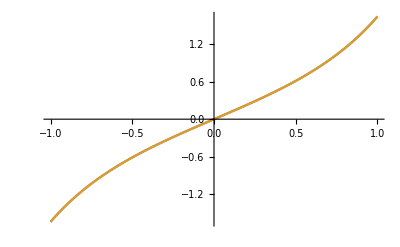

```mathematica
Plot[{Erfi[x],-I Erf[I x]},{x,-1,1}]
```

```mathematica
Limit[-(ⅇ^(-η κ) v0^2 μ Erfi[√η √(-2+κ)])/(√π √(-2+κ) λ Erf[√Y]^2),κ->0]
```

-Erf[√2 √η]/(√(2 π) Erf[√Y]^2)

```mathematica
DSolve[D[ζ[η],η]+κ ζ[η] ==0,ζ[η],η]
```

{{ζ[η]→ⅇ^(-η κ) C[1]}}

```mathematica
Limit[ⅇ^(-η κ) C[1]-(ⅇ^(-η κ) v0^2 μ Erfi[√η √(-2+κ)])/(√π √(-2+κ) λ Erf[√Y]^2),η->0]
```

C[1]

```mathematica
DSolve[Sqrt[η]D[θ[η],η] ==ⅇ^(-η κ) C[1],θ[η],η]
```

{{θ[η]→C[2]+(√π C[1] Erf[√η √κ])/(√κ)}}

```mathematica
Limit[C[2]+(√π C[1] Erf[√η √κ])/(√κ),η->Y]
```

```mathematica
Limit[C[2]+(√π C[1] Erf[√η √κ])/(√κ),η->Infinity]
```

```mathematica
Limit[C[2]+(√π C[1] Erf[√η ])/(√κ),η->∞]
```

(√π C[1])/(√κ)+C[2]

```mathematica
FullSimplify[Solve[{C2+(√π C1 Erf[√Y √κ])/(√κ)==Θ,(√π C1)/(√κ)+C2==0},{C1,C2}]]
```

{{C1→-(Θ √κ)/(√π Erfc[√Y √κ]),C2→Θ/Erfc[√Y √κ]}}

```mathematica
FullSimplify[-(Θ √κ)/(√π Erfc[√Y √κ])ⅇ^(-η κ) ]
```

-(ⅇ^(-η κ) Θ √κ)/(√π Erfc[√Y √κ])

```mathematica
Integrate[Erf[ Sqrt[ x]] Exp[-b x]/Sqrt[x],x]
```

-(√π (1+4 OwenT[√2 √b √x,1/(√b)]))/(√b)

```mathematica
Manipulate[Plot[Re[-(√π (1+4 OwenT[√2 √b √x,1/(√b)]))/(√b)],{x,0,10}],{b,-10,0}]
```

```mathematica
D[-(√π (1+4 OwenT[√2 √b x,1/(√b)]))/(√b),x]
```

2 ⅇ^(-b x^2) Erf[x]